## SubHorizon Kernel limit (x>>1)

```mathematica
y[d_,s_]:=-1-(2(1-d^2))/((d+s)(d-s));
```

```mathematica
(*Olver's function in terms of hypergeometrics*)
Olver[n_,m_,x_]:=Pi/(2Sin[m*Pi]Gamma[n+m+1])(((x+1)/(x-1))^(m/2)Hypergeometric2F1[n+1,-n,1-m,(1-x)/2]/Gamma[1-m]-Gamma[n+m+1]/Gamma[n-m+1]((x-1)/(x+1))^(m/2)Hypergeometric2F1[n+1,-n,1+m,(1-x)/2]/Gamma[1+m]);
```

```mathematica
(*The kernel, in the subhorizon limit*)SubLimitI[x_,c_,b_,d_,s_]:=x^(-b-1)4^(b+1)Gamma[b+3/2]^2(2b+3)/(b+2)(Abs[1-y[d,s]^2]^(b/2))/((d+s)(s-d))*(Cos[x-(b*Pi)/2]*(LegendreP[b,-b,y[d,s]]+(b+2)/(b+1)LegendreP[b+2,-b,y[d,s]])*HeavisideTheta[s-1]+2/Pi Sin[x-(b*Pi)/2]*(LegendreQ[b,-b,y[d,s]]+(b+2)/(b+1)LegendreQ[b+2,-b,y[d,s]])*HeavisideTheta[s-1]-2/Pi Sin[x-(b*Pi)/2](Olver[b,-b,-y[d,s]]+(b+2)/(b+1)Olver[b+2,-b,-y[d,s]])*HeavisideTheta[1-s]);
```

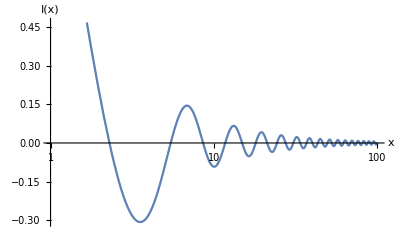

```mathematica
LogLinearPlot[SubLimitI[x,0.3,0.2,0.1,2],{x,1,100},AxesLabel->{"x","I(x)"}]
```

## SuperHorizon Kernel limit (x<<1)

```mathematica
B1b[b_,c_,v_]:=-((3+2b)^2(1+b+b^2))/(4b(1+b)^2(2+b))(c*v)^-2;
B2b[b_,c_,v_]:=(4^(1+b)Gamma[b+5/2]^2)/(b(1+b)(2+b)Pi)(c*v)^(-2(1+b));
```

```mathematica
SuperLimitI[b_,c_,v_,x_]:=B1b[b,c,v]+B2b[b,c,v]*x^(-2b);
```

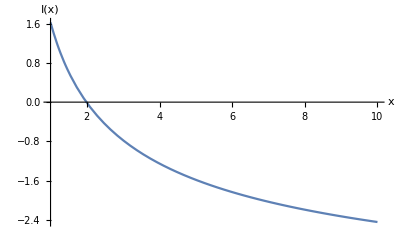

```mathematica
Plot[SuperLimitI[0.2,0.3,2.1/0.6,x],{x,1,10},AxesLabel->{"x","I(x)"}]
```